## Details

### Capabilities

The Phylogenetics` package can:

 - parse a Newick tree string to a Mathematica-usable Tree object and write a Tree object to a Newick string;
 - parse a Cluster object of the HierarchicalClustering` package to a Tree and convert a Tree to Cluster representation;
 - test properties of Tree objects;
 - extract vertices, edges, internal nodes, leafs, sub- and supertrees of Tree objects;
 - directly calculate various properties of Tree objects like paths and distances between vertices;
 - convert a Tree object to Graph, and a tree Graph to Tree; any tree graph (TreeGraph, ClusteringTree, etc.) for which TreeGraphQ returns True can be converted to Tree;
 - convert a Tree object or a Graph tree to Cladogram graph,
 - provide example trees in Newick and Cluster format.

### Tree specification

A phylogenetic tree can be represented in many ways. The Newick format is a minimal comma-bracket string descriptor of a directed tree (see the Newick Standard and this site for syntax details, here is an online tree visualizer). A simple Newick string example is resolved as follows:

"(A:0.1,B:0.2,(C:0.3,D:0.4)E:0.5)F;"

-Graphics-

Where numbers indicate branch lengths between connected parent-child nodes. The unit (b_1, b_2, ...)n represents a tree, rooted at node n with branches b_i in parenthesis. Branch b_i can be a tree itself or a leaf node. Any node can have a label lbl and a distance d to its parent in the form lbl:d. Multiple, independent trees can be separated by a semicolon (;). The Newick format is rather flexible, as is apparent from the wiki. Both the label and the distance can be omitted for nodes, hence a pure comma-bracket string like ((,),,) is a valid tree with unnamed nodes and unit distances.

The above Newick string is converted to a Tree object that basically inherits the Newick structure, but is a full representation where nothing is omitted:

Tree[F, {A, B, Tree[E, {C, D}]}]

which is represented in StandardForm output as:

Tree["F",{"A","B",Tree["E",{"C","D"}]}]

A Tree object is a description of a tree graph, a directed, acyclic graph, that always has a root vertex with name n and can contain branches b_i (polytomies, singular branches or no branches are allowed at any branching):

Tree[n, {b_1, b_2, …}]

The root of a tree is always a vertex, but a branch can be a vertex or a Tree. Vertices (internal nodes and leafs) are represented as associations, containing the following information:

<|"Name" → F, "Label" → F, "BranchLength" → 1, "Type" → "Node"|>

"Name" specifies the unique name of the vertex, just like in Graph.
"Label" specifies the label of the vertex that might appear when the tree is displayed as a graph.
"BranchLength" specifies the distance of the vertex to its parent vertex.
"Type" specifies the type of the vertex: Node indicates an internal node, Leaf indicates a terminal node.
Additional vertex-specific properties can be easily added, by editing the vertex-specification ($TreeVertexProperties).

### Further notes

- A Newick tree is right associative: "(b)a" is the valid specification instead of "a(b)". The latter is not recognized correctly.
- Polytomies are allowed in a Newick string (and in a Tree) at any level in the form of "(a,b,c)d".
- If no distance is specified for a node to its parent, it is assumed to be 1.
- If the distance of a node is 0, when visualized, it can appear on top of its parent node, possibly covering it.
- If a node label is not specified, it is assumed to be None. When converting to Tree format (and to Graph or Cladogram), all nodes are resolved to have unique names, and labels are added as VertexLabels.
- TreeToGraph and Cladogram return Graph objects, with all the Graph functionalities.
- TreeGraph represent the distance of nodes along the branching dimension (i.e. the y coordinate) by vertex weights using VertexWeight; Cladogram does the same.
- Cladogram stores the stem lengths as EdgeWeight.
- Since the vertex positions represent important information of the graph (e.g. similarity or evolutionary distance of vertices), they must be explicitly represented and not distorted by e.g. AspectRatio.
- Conversion from Graph to Tree and back does not necessarily result in the same vertex indices as a Tree is always parsed from root to leaves while a graph may not be parsed the same way by Mathematica when indexing vertices.

### Sources

- The Newick Standard: http://evolution.genetics.washington.edu/phylip/newicktree.html
- Wikipedia: Newick format: https://en.wikipedia.org/wiki/Newick_format
- Newick tree formats: http://marvin.cs.uidaho.edu/Teaching/CS515/newickFormat.html
- An online Newick tree visualizer: http://etetoolkit.org/treeview/
- Orthogonal EdgeShapeFunction by Vitaliy Kaurov: http://community.wolfram.com/groups/-/m/t/241376

## Package initialization

Load the Phylogenetics` package and check its version number.

```mathematica
Needs["Phylogenetics`"];
$PhylogeneticsVersionNumber
```

1.1

Set some options for plotting trees.

```mathematica
SetOptions[#,VertexLabelStyle->White,EdgeLabelStyle->Orange,EdgeStyle->Thick]&/@{Cladogram,Graph,TreeGraph};
```

Available functions within the Phylogenetics` package.

```mathematica
Information["Phylogenetics`*"]
```

## Trees

NewickToTree parses a Newick string and returns a Tree object.

```mathematica
tree=NewickToTree["(A:0.1,B:0.2,((G:.1,H:0.2,I:0.3)C:0.3,D:0.4)E:0.5)F;"]
```

Tree[F,{A,B,Tree[E,{Tree[C,{G,H,I}],D}]}]

Visualize the tree.

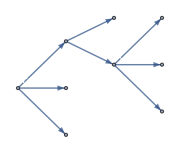

```mathematica
TreeToGraph[tree,ImageSize->Small]
```

Select and copy the full output Tree object and use it as input. Make sure, that you select the whole expression.

```mathematica
TreeToGraph[Tree["F",{"A","B",Tree["E",{Tree["C",{"G","H","I"}],"D"}]}],ImageSize->Small]
```

-Graphics-

Query all vertices, leaf or internal node vertices of the tree.

```mathematica
{VertexList[tree],LeafList@tree,NodeList[tree]}
```

{{F,A,B,E,C,G,H,I,D},{A,B,G,H,I,D},{F,E,C}}

Query the branch length of all nodes or for a selected set of nodes.

```mathematica
{BranchLength[tree],BranchLength[tree,{"F","B","C"}]}
```

{{1,0.1,0.2,0.5,0.3,0.1,0.2,0.3,0.4},{1,0.2,0.3}}

Return the vertices of subtrees rooted at specific nodes.

```mathematica
{VertexList[Subtree[tree,"C"]],VertexList[Subtree[tree,"A"]],VertexList[Subtree[tree,"F"]]}
```

{{C,G,H,I},{A},{F,A,B,E,C,G,H,I,D}}

Query the edge list of a tree.

```mathematica
EdgeList[tree]
```

{F→A,F→B,F→E,E→C,E→D,C→G,C→H,C→I}

Display tree as a table of nodes.

```mathematica
FullVertexList[tree]//Dataset
```

Dataset[<>]

## Indices

DistanceIndex lists the absolute distance of each node from the absolute root at distance 0. Note, that the explicit root D has a distance of 4 from the unspecified implicit root.

```mathematica
DistanceIndex[NewickToTree["(((A:1)B:2)C:3)D:4;"]]
```

<|D→4,C→7,B→9,A→10|>

If no distance is specified for the explicit root vertex (D), it is assumed to be 1.

```mathematica
DistanceIndex[NewickToTree["(((A:1)B:2)C:3)D;"]]
```

<|D→1,C→4,B→6,A→7|>

Specify a node to be the absolute root by assigning a branch length of 0.

```mathematica
DistanceIndex[NewickToTree["(((A:1)B:2)C:3)D:0;"]]
```

<|D→0,C→3,B→5,A→6|>

DescendantIndex lists all the vertices below each vertex in topological (depth-first) order.

```mathematica
tree=NewickToTree["(A:0.1,B:0.2,((G:.1,H:0.2,I:0.3)C:0.3,D:0.4)E:0.5)F:0.3;"];
DescendantIndex[tree]
```

<|F→{A,B,E,C,G,H,I,D},E→{C,G,H,I,D},D→{},C→{G,H,I},I→{},H→{},G→{},B→{},A→{}|>

AncestorIndex returns all the direct ancestors of vertices in the tree in topological order, starting from the root.

```mathematica
AncestorIndex[tree]
```

<|F→{},A→{F},B→{F},G→{F,E,C},C→{F,E},E→{F},H→{F,E,C},I→{F,E,C},D→{F,E}|>

ChildIndex lists all the vertices immediately below each vertex.

```mathematica
ChildIndex[tree]
```

<|F→{A,B,E},E→{C,D},D→{},C→{G,H,I},I→{},H→{},G→{},B→{},A→{}|>

BranchLengthIndex lists the branch length values for each vertex (i.e. the distance of the vertex to its parent node).

```mathematica
BranchLengthIndex[tree]
```

<|F→0.3,A→0.1,B→0.2,E→0.5,C→0.3,G→0.1,H→0.2,I→0.3,D→0.4|>

## TreeDistanceMatrix

Display parent-child node distances stored in a tree as edgelabels in a cladogram.

```mathematica
tree=NewickToTree["(A:0.1,B:0.2,((G:.1,H:0.2,I:0.3)C:0.3,D:0.4)E:0.5)F;"];
Cladogram[tree,ImageSize->Small,EdgeLabels->"EdgeWeight"]
```

-Graphics-

Return all the pairwise distances of the tree as a matrix.

```mathematica
TreeDistanceMatrix[tree]//MatrixForm
```

(0 | 0.1 | 0.2 | 0.5 | 0.8 | 0.9 | 1. | 1.1 | 0.9
0.1 | 0 | 0.3 | 0.6 | 0.9 | 1. | 1.1 | 1.2 | 1.
0.2 | 0.3 | 0 | 0.7 | 1. | 1.1 | 1.2 | 1.3 | 1.1
0.5 | 0.6 | 0.7 | 0 | 0.3 | 0.4 | 0.5 | 0.6 | 0.4
0.8 | 0.9 | 1. | 0.3 | 0 | 0.1 | 0.2 | 0.3 | 0.7
0.9 | 1. | 1.1 | 0.4 | 0.1 | 0 | 0.3 | 0.4 | 0.8
1. | 1.1 | 1.2 | 0.5 | 0.2 | 0.3 | 0 | 0.5 | 0.9
1.1 | 1.2 | 1.3 | 0.6 | 0.3 | 0.4 | 0.5 | 0 | 1.
0.9 | 1. | 1.1 | 0.4 | 0.7 | 0.8 | 0.9 | 1. | 0)

Query the distance matrix of a specific subset of vertices.

```mathematica
v={"F","F","A","H"};
MatrixForm[TreeDistanceMatrix[tree,v],TableHeadings->{v,v}]
```

( | F | F | A | H
F | 0 | 0 | 0.1 | 1.
F | 0 | 0 | 0.1 | 1.
A | 0.1 | 0.1 | 0 | 1.1
H | 1. | 1. | 1.1 | 0)

## Layout

Display trees as graphs subject to different layouts.

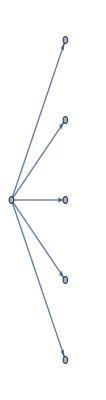
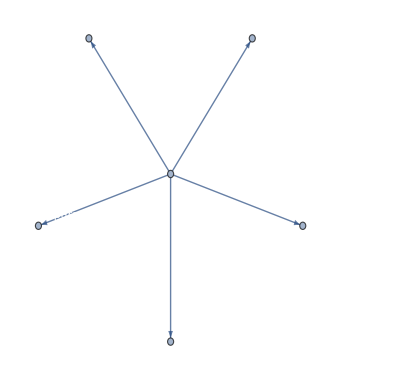
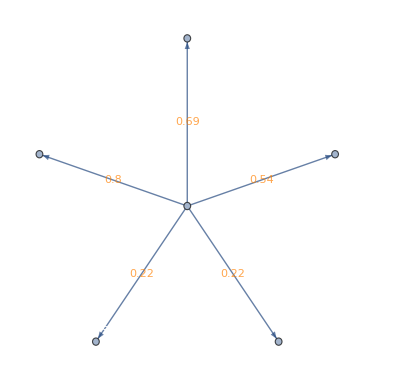
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
tree=NewickToTree[PhylogeneticData["NewickSaccharomyces"]];
{
TreeToGraph[tree,VertexLabelStyle->White],
TreeToGraph[tree,VertexLabelStyle->White,GraphLayout->"RadialDrawing"],TreeToGraph[tree,EdgeLabels->Automatic,VertexLabelStyle->White,GraphLayout->{"StarEmbedding","Center"->Automatic},EdgeLabels->"EdgeWeight",EdgeLabelStyle->Orange],
Cladogram[tree,EdgeLabels->Automatic,ImagePadding->{{5,50},{5,10}}]
}
```

Cladogram is a graph object.

```mathematica
Head[Cladogram[tree]]
```

Graph

A Cladogram is a directed graph, with directed edges.

```mathematica
DirectedGraphQ[Cladogram[tree]]
Cladogram[tree]//EdgeList
```

True

{1->S.cerevisiae,1->S.paradoxus,1->S.mikatae,1->S.kudriavzevii,1->S.bayanus}

Display the tree in different layouts.

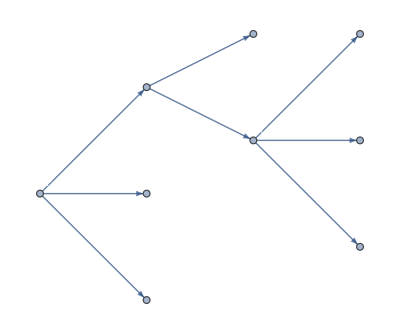
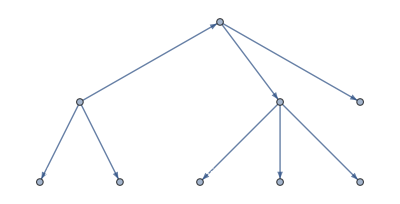
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
tree=NewickToTree[PhylogeneticData["ExampleNewick"]];
{
TreeToGraph[tree,VertexLabelStyle->White,ImagePadding->10],
TreeGraph[VertexList[tree],EdgeList[tree],VertexLabels->"Name"],
Cladogram[tree,EdgeLabels->Automatic,Frame->True,LayerSizeFunction->(1#&),ImageSize->Medium]
}
```

## Conversion to/from Newick format

Converting from Newick string to tree and back should yield the same string.

```mathematica
old="(((a,(,,),a3)b))d:1.4;";
new=TreeToNewick[NewickToTree[old]]
old===new
```

(((a,(,,),a3)b))d:1.4;

True

Unnamed or identical nodes are assigned unique indices to avoid collision.

```mathematica
tree=NewickToTree["((a,,b)a)"]
```

Tree[1,{Tree[a,{2,3,b}]}]

Labels are nevertheless retained and can be accessed by VertexLabels.

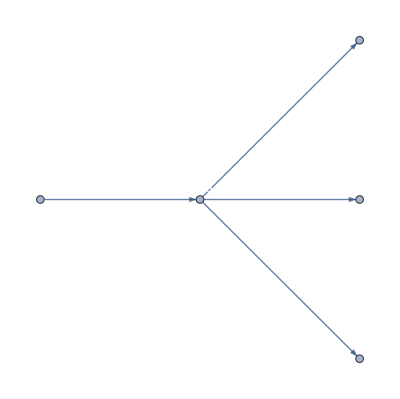

```mathematica
g=TreeToGraph[tree,ImageSize->Tiny]
```

```mathematica
PropertyValue[g,VertexLabels]
```

{3→None,b→b,a→a,2→a,1→None}

## Conversion to and from hierarchical cluster format

Convert a hierarchical clustering structure to a tree.

```mathematica
cluster=PhylogeneticData["ExampleCluster1"]
tree=ClusterToTree[cluster]
```

Cluster[Cluster[Cluster[a,Cluster[h,j,1.52217,1,1],28.8538,1,2],Cluster[Cluster[c,e,10.1371,1,1],d,22.0063,2,1],47.1129,3,3],Cluster[Cluster[b,Cluster[g,i,2.5374,1,1],5.73533,1,2],f,13.6197,3,1],64.5168,6,4]

Tree[1,{Tree[2,{Tree[4,{a,Tree[7,{h,j}]}],Tree[5,{Tree[8,{c,e}],d}]}],Tree[3,{Tree[6,{b,Tree[9,{g,i}]}],f}]}]

A hierarchical clustering structure is always binary, therefore if it is converted to Tree, the result will always be strictly binary.

```mathematica
BinaryTreeQ[tree]
```

True

Visualize the tree.

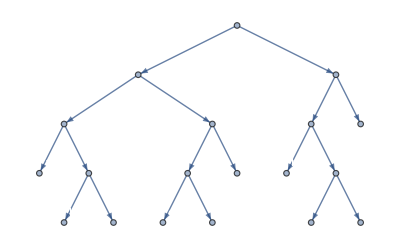
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{TreeToGraph[tree,GraphLayout->{"LayeredEmbedding",Orientation->Top}],
Cladogram[tree,Orientation->Top,ImageSize->Small,ImagePadding->10],
DendrogramPlot[cluster,Orientation->Top,LeafLabels->(Style[#,White]&),PlotStyle->White]}
```

Convert back to cluster format.

```mathematica
new=TreeToCluster[tree]
```

Cluster[Cluster[Cluster[a,Cluster[h,j,1.52217,1,1],28.8538,1,2],Cluster[Cluster[c,e,10.1371,1,1],d,22.0063,2,1],47.1129,3,3],Cluster[Cluster[b,Cluster[g,i,2.5374,1,1],5.73533,1,2],f,13.6197,3,1],64.5168,6,4]

Conversion from and to cluster format should result in the same tree topology and values up to numerical precision. Therefore, instead of SameQ, Equal should be used when comparing objects.

```mathematica
{cluster===new,cluster==new}
```

{False,True}

## Subtree

Subtree returns the tree that is rooted at the requested node.

```mathematica
tree=NewickToTree["(A:0.1,B:0.2,((G:.1,H:0.2,I:0.3)C:0.3,D:0.4)E:0.5)F;"]
Subtree[tree,"C"]
```

Tree[F,{A,B,Tree[E,{Tree[C,{G,H,I}],D}]}]

Tree[C,{G,H,I}]

If the vertex is a leaf, it is returned wrapped in Tree (with zero branches), so that it can be converted to Graph more easily by other functions.

```mathematica
Subtree[tree,"H"]
```

Tree[H,{}]

If the vertex is not present in the tree, Missing is returned.

```mathematica
Subtree[tree,"X"]
```

Missing[NotFound]

GraphHighlight, besides graphs, edges and vertices, works also with Tree objects in Cladogram.

```mathematica
Cladogram[tree,GraphHighlight->Subtree[tree,#],PlotLabel->#,VertexLabels->"Name"]&/@{"F","E","C","A"}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Supertree

Supertree returns the most compact subtree of a tree that includes all listed vertices.

```mathematica
tree=NewickToTree["(A:0.1,B:0.2,((G:.1,H:0.2,I:0.3)C:0.3,D:0.4)E:0.5)F;"]
```

Tree[F,{A,B,Tree[E,{Tree[C,{G,H,I}],D}]}]

```mathematica
Supertree[tree,{"H","I"}]
```

Tree[C,{G,H,I}]

Supertree works with any vertex, leaf or internal node.

```mathematica
Supertree[tree,{"H","A","C"}]
```

Tree[F,{A,B,Tree[E,{Tree[C,{G,H,I}],D}]}]

The supertree of a leaf vertex consists only itself, wrapped in Tree.

```mathematica
Supertree[tree,"G"]
```

Tree[G,{}]

An unknown vertex does not have a supertree.

```mathematica
Supertree[tree,"X"]
```

Missing[NotFound]

Visualize supertrees as highlighted subgraphs.

```mathematica
Cladogram[tree,ImageSize->Small,GraphHighlight->Supertree[tree,#],PlotLabel->#,VertexLabels->"Name"]&/@{{"A","D"},{"H","I","C","D"},{"I","G"},"G"}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## CommonAncestor

The common ancestor of two leaves is the internal node of the tree where they branch off.

```mathematica
tree=NewickToTree["(A:0.1,B:0.2,((G:.1,H:0.2,I:0.3)C:0.3,D:0.4)E:0.5)F;"]
CommonAncestor[tree,{"H","G"}]
```

Tree[F,{A,B,Tree[E,{Tree[C,{G,H,I}],D}]}]

C

The common ancestor of multiple nodes is the root of the smallest subtree inclusive of all listed vertices.

```mathematica
CommonAncestor[tree,{"H","G","D"}]
```

E

A common ancestor of a single node is itself.

```mathematica
CommonAncestor[tree,"E"]
```

E

## DivergenceTime

The divergence time of two vertices is the absolute distance of their common ancestor from the absolute, implicit root node (at distance 0).

```mathematica
tree=NewickToTree["(A:0.1,B:0.2,((G:.1,H:0.2,I:0.3)C:0.3,D:0.4)E:0.5)F;"]
d=DivergenceTime[tree,{"H","G"}]
```

Tree[F,{A,B,Tree[E,{Tree[C,{G,H,I}],D}]}]

1.8

```mathematica
Cladogram[tree,Frame->True,LayerSizeFunction->(1#&),GridLines->{{{d,Dashed}},{}},GraphHighlight->Supertree[tree,{"H","G"}]]
```

-Graphics-

The divergence time of multiple vertices is the absolute time of the internal node that is the root of the smallest subtree containing all vertices.

```mathematica
DivergenceTime[tree,{"H","G","D"}]
```

1.5

The divergence time of a single vertex is its absolute distance.

```mathematica
DivergenceTime[tree,"E"]
```

1.5

## Paths and distances

The path between two nodes is always the shortest path.

```mathematica
tree=NewickToTree["(A:0.1,B:0.2,((G:.1,H:0.2,I:0.3)C:0.3,D:0.4)E:0.5)F;"];
TreePath[tree,"G","D"]
```

{C→G,E→C,E→D}

The pair of vertices can be also provided as a list.

```mathematica
TreePath[tree,{"G","D"}]
```

{C→G,E→C,E→D}

A single vertex returns a path from the root.

```mathematica
TreePath[tree,"G"]
```

{C→G,E→C,F→E}

A path between a vertex and itself returns the vertex.

```mathematica
TreePath[tree,"G","G"]
```

G

The path to an unknown vertex is an empty list.

```mathematica
TreePath[tree,"G","X"]
```

{}

The distance between two nodes is the summed branch lengths of the shortest path.

```mathematica
TreeDistance[tree,"G","D"]
```

0.8

The pair of vertices can be also provided as a list.

```mathematica
TreeDistance[tree,{"G","D"}]
```

0.8

A single vertex returns its absolute distance from the root.

```mathematica
TreeDistance[tree,"G"]
```

0.9

A distance between a vertex and itself is always 0.

```mathematica
TreeDistance[tree,"G","G"]
```

0

Distance to an unknown vertex is infinite.

```mathematica
TreeDistance[tree,"G","X"]
```

∞

The distance of two nodes is always a nonnegative value, regardless of the direction.

```mathematica
{TreeDistance[tree,{"F","I"}],TreeDistance[tree,{"I","F"}]}
```

{1.1,1.1}

Examples.

```mathematica
list={{"I","F"},{"F","I"},{"H","H"},{"H","G"},{"G","D"},{"H","B"},{"C"},{"X"}};
path=TreePath[tree,#]&/@list;
dist=TreeDistance[tree,#]&/@list;
MapThread[Cladogram[tree,GraphHighlight->#1,ImageSize->Small,PlotLabel->Row@{#1,": ",#2}]&,{path,dist}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Clusters

Clusterize a list of strings based on their similarity. Cladogram cannot work with such lists directly, but can accept the graph produced by ClusteringTree. Since Dendrogram returns a static Graphics object instead of a rich Graph, Cladogram cannot deal with it.

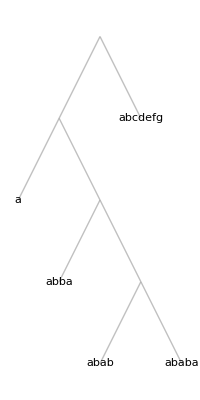
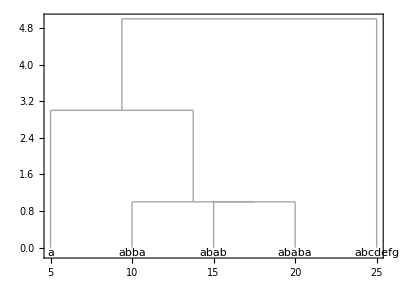
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
list={"a", "abba","abab", "ababa", "abcdefg"};
{
g=ClusteringTree[list,VertexLabelStyle->Black],
Dendrogram[list,Frame->True,PlotRangePadding->Scaled[.15]],
Cladogram[g,Orientation->Top,Frame->True,ImagePadding->All,PlotRangePadding->Scaled[.1],VertexLabelStyle->Black]
}
```

Since Cladogram measures distances from the root instead of (dis)similarity between vertices, the result is a mirrorred plot. To display it correctly, invert the vertex weights that represent the vertical absolute distance for each node.

```mathematica
w=PropertyValue[c,VertexWeight]
Cladogram[g,VertexWeight->(Max@w-w),Orientation->Top,Frame->True,ImagePadding->All,ImageSize->Small,PlotRangePadding->Scaled[.1],VertexLabelStyle->Black]
```

{5.,3.,0,1.,0,1.,0,0,0}

-Graphics-

## Graphs

Display a tree as a graph in various ways and layouts.

Tree[1,{Tree[2,{Tree[4,{8}],5}],Tree[3,{6,7}]}]

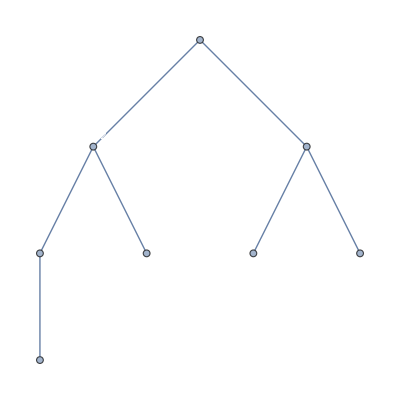
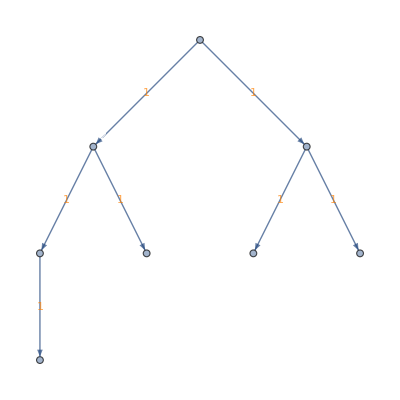
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
g=KaryTree[8,DirectedEdges->False,VertexLabels->"Index",VertexLabelStyle->White];
tree=GraphToTree[g]
{
g,
TreeToGraph[tree,VertexLabelStyle->White,GraphLayout->{"LayeredEmbedding","Orientation"->Top,"RootVertex"->1},EdgeLabels->"EdgeWeight",EdgeLabelStyle->Orange],
Cladogram[tree,Orientation->Top,EdgeLabels->"EdgeWeight"],
Cladogram[g,Orientation->Top,EdgeLabels->"EdgeWeight"]
}
```

Display some example graphs as cladograms.

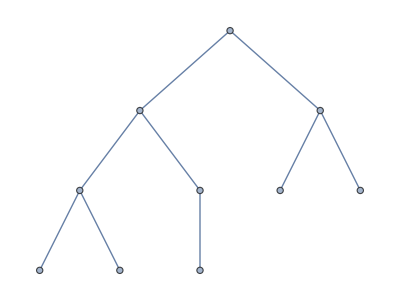
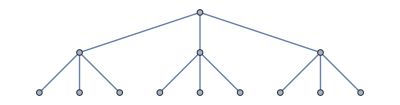
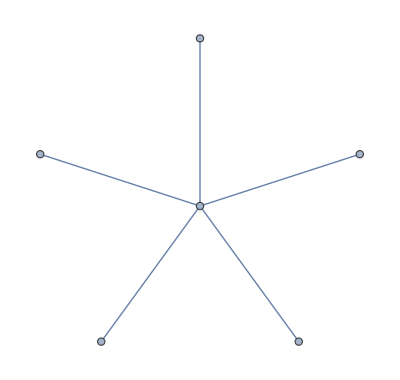
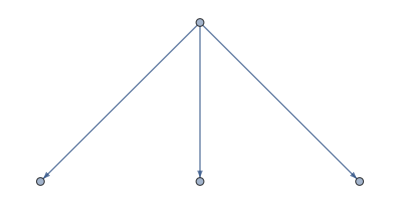

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
graphs={KaryTree[10],CompleteKaryTree[3,3],StarGraph[6],TreeGraph[{1->2,1->3,1->4}]}
Cladogram[#,Orientation->Top]&/@graphs
```

## Phylogenetic data

List the available phylogenetic examples stored within PhylogeneticData.

```mathematica
all=PhylogeneticData["Names"]
```

{ExampleNewick,ExampleNewick1,ExampleNewick2,ExampleNewick3,ExampleNewick6,ExampleNewick7,ExampleNewick8,ExampleNewick9,ExampleNewickEmpty1,ExampleNewickEmpty2,ExampleNewickEmpty3,ExampleNewickEmpty4,ExampleCluster1,ExampleCluster2,NewickMammal1,NewickMammal2,NewickMammal3,NewickHominoid,NewickSaccharomyces,NewickEukarya}

Display example data.

```mathematica
Cladogram[If[StringMatchQ[#,"*Newick*"],NewickToTree,ClusterToTree]@PhylogeneticData[#],ImageSize->Small,PlotLabel->#]&/@Most[all]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

A complex tree, showing the diversificaion of Eukarya, with Metazoa highlighted (from Parfrey et al. 2011).

```mathematica
tree=NewickToTree[PhylogeneticData["NewickEukarya"]];
Cladogram[tree,ImageSize->500,ImagePadding->{{1,100},{1,1}},LayerSizeFunction->(1/5#&),VertexSize->.3,VertexLabelStyle->Directive[White,9,Italic],GraphHighlight->Supertree[tree,{"Nematostella_vectensis","Homo_sapiens"}]]
```

-Graphics-